```mathematica
B = {{10, 0, 0}, {0, 20, 0}, {0,0,30}}
```

{{10,0,0},{0,20,0},{0,0,30}}

```mathematica
MatrixForm[B]
```

(10 | 0 | 0
0 | 20 | 0
0 | 0 | 30)

```mathematica
A = {{0,1,1},{1,0,0},{1,0,0}}
```

{{0,1,1},{1,0,0},{1,0,0}}

```mathematica
MatrixForm[A]
```

(0 | 1 | 1
1 | 0 | 0
1 | 0 | 0)

```mathematica
H = B - A
```

{{10,-1,-1},{-1,20,0},{-1,0,30}}

```mathematica
MatrixForm[H]
```

(10 | -1 | -1
-1 | 20 | 0
-1 | 0 | 30)

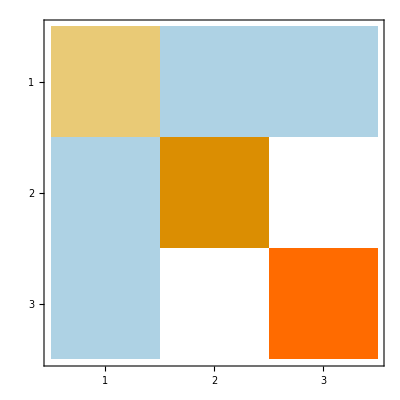

```mathematica
MatrixPlot[H]
```

```mathematica
Eigenvalues[H]
```

{Root30.1Root[-5950+1098 #1-60 #1^2+#1^3&,3]30.0501237493043,Root20.1Root[-5950+1098 #1-60 #1^2+#1^3&,2]20.0980484567532,Root9.85Root[-5950+1098 #1-60 #1^2+#1^3&,1]9.8518277939425}

```mathematica
s =  EigenSystem[H]
```

EigenSystem[{{10,-1,-1},{-1,20,0},{-1,0,30}}]

Analytically, we can find that the characteristic polynomial of the Hamiltonian is simply:

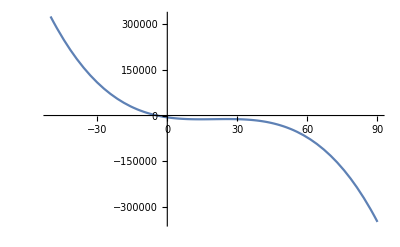

```mathematica
Plot[-x^3+60x^2-1098x-5990, {x, -50, 90}]
```

## Unitary Evolution Checks:

Now, we’ll check that the unitary evolution implemented in the AndersonGraph.py class is mathematically. The example of the star graph is taken as prototypical. We work out this example fully to ensure the mechanics of the code are within functioning parameters.

```mathematica
P = MatrixExp[H*I*#1, #2]&
```

MatrixExp[H ⅈ #1,#2]&

```mathematica
ψ = {0, 1, 0}
```

{0,1,0}

```mathematica
P[1, ψ]
```

{-1/3 RootSum[-5950+1098 #1-60 #1^2+#1^3&,(-30 ⅇ^(ⅈ #1)+ⅇ^(ⅈ #1) #1)/(366-40 #1+#1^2)&],1/3 RootSum[-5950+1098 #1-60 #1^2+#1^3&,(299 ⅇ^(ⅈ #1)-40 ⅇ^(ⅈ #1) #1+ⅇ^(ⅈ #1) #1^2)/(366-40 #1+#1^2)&],1/3 RootSum[-5950+1098 #1-60 #1^2+#1^3&,ⅇ^(ⅈ #1)/(366-40 #1+#1^2)&]}

5